```mathematica
Clear["Global`*"]
```

```mathematica
Below are a bunch of built-in functions (from MAR_mulitank);

(*RowDelete takes a matrix and deletes the specified rows*)
RowDelete[x_,entries_]:=Module[{list},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]

(*ColumnDelete will take a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]

(*AddZeroToRow will, you guessed it, add a zero to a row vector! Wherever you want it!*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]

(*AddZerosToRow will add any number of zeros to a row vector in any places you want.*)
AddZerosToRow[x_,entries_]:=Module[{y,list},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]
```

```mathematica
(*This generates multiple datasets (tanks) where the noise terms driving all tanks are uncorrelated. This is probably more realistic.*)

GenerateUnCorrelatedDatasets[A_,B_,q_,time_]:=Module[{a,b,p,noise,x0,X0,X},
p=Length[B[[1]]];
a=A[[All,1]];
b=Transpose[B];
X={};
For[j=1,j≤q,j++,
noise=Table[RandomVariate[NormalDistribution[],p],{j,1,time+1}];
x0=RandomVariate[UniformDistribution[{-1,1}],p];
X0={x0};
For[t=1,t≤time,t++;
x0=a+x0.b+5noise[[t]];
X0=Join[X0,{x0}]
];
X=Join[X,{X0}]
];
X
]

(*Unconstrained estimate with covariates. For input we need to know how many covariates there are. Zero covariates are fine.*)
CompUnConstrainedCov[datasets_,cov_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata},
p=Length[datasets[[1,1]]]-cov;
If[cov==0,

X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
d0={Y[[All,k]]}.Z.Inverse[Transpose[Z].Z];
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
d0={Y[[All,k]]}.Z.Inverse[Transpose[Z].Z];
D=Join[D,d0]
];
D
]
]


(*Composite constrained and unconstrained estimates with covatiares. I.e., the most general case.*)

MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]
```

```mathematica
(*Experiments are below. You can change any of the main parameters (A, B, q = number of tanks,finaltime = length of timeseries). Just try to be sure that your B matrix is stable: all eigenvalues should be less than one in absolute value.*)
```

```mathematica
(*Experiment with UNCorrelated datasets*)

A={{-.2},{1.0},{.5}};
B={{.8,-.2,0},{-.1,.5,.1},{.1,0,.4}};
p=Length[B[[1]]];
q=4;
finaltime=30;

datasets=GenerateUnCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
]

AvgD=Mean[Mlist];


Print["Dmatrix = "MatrixForm[A],MatrixForm[B]]
Print["Comp= ",MatrixForm[CompD]," Avg = "MatrixForm[AvgD]]
Print["Eigenvalues = ",Eigenvalues[B]," -- ",Abs[Eigenvalues[CompD[[All,2;;p+1]]]]," -- ",Abs[Eigenvalues[AvgD[[All,2;;p+1]]]]]
Print["Stability = ",Det[B]^(2/p)," -- ", Det[CompD[[All,2;;p+1]]]^(2/p), " -- ",  Det[AvgD[[All,2;;p+1]]]^(2/p)]
```

Dmatrix =  (-0.2
1.
0.5)(0.8 | -0.2 | 0
-0.1 | 0.5 | 0.1
0.1 | 0 | 0.4)

Comp= (0.40043 | 0.762447 | -0.302413 | 0.0253701
0.95815 | -0.274072 | 0.204119 | 0.226287
0.490632 | 0.130449 | -0.0313638 | 0.30338) Avg =  (0.137294 | 0.664172 | -0.190348 | 0.0548807
0.597568 | -0.17758 | 0.12159 | 0.25868
0.696913 | 0.142109 | -0.0859462 | 0.255346)

Eigenvalues = {0.844949,0.5,0.355051} -- {0.867932,0.34084,0.0611743} -- {0.711741,0.166149,0.166149}

Stability = 0.282311 -- 0.0689292 -- 0.0728133

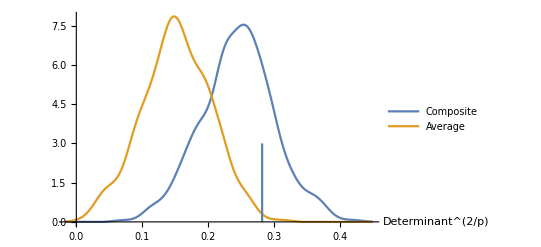

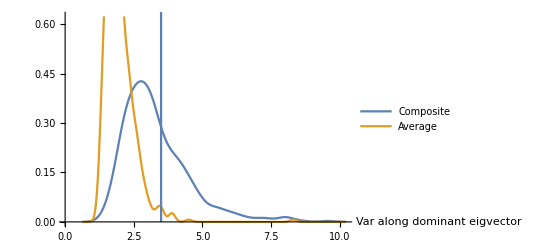

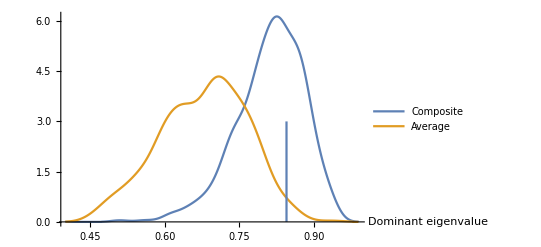

```mathematica
(*Comparison of methods for UNcorrelated datasets. Here you will see there is huge difference.*)

A={{-.2},{1.0},{.5}};
B={{.8,-.2,0},{-.1,.5,.1},{.1,0,.4}};


(*
A={{1.0},{.5}};
B={{.4,-.2},{-.1,.5}};
*)

p=Length[B[[1]]];
q=4;
finaltime=30;

runs=500;

DetComp={};DetAvg={};
VarComp={};VarAvg={};
EigenComp={};EigenAvg={};

For[r=1,r≤runs,r++,
datasets=GenerateUnCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];
DetComp=Join[DetComp,{Det[CompD[[All,2;;p+1]]]}];
VarComp=Join[VarComp,{1/(1-(Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]])^2)}];
EigenComp=Join[EigenComp,{Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]]}];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
];

AvgD=Mean[Mlist];
DetAvg=Join[DetAvg,{Det[AvgD[[All,2;;p+1]]]}];
VarAvg=Join[VarAvg,{1/(1-(Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]])^2)}];
EigenAvg=Join[EigenAvg,{Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]]}]
]

Show[SmoothHistogram[{(DetComp^2)^(1/p),(DetAvg^2)^(1/p)},  PlotLegends->{"Composite","Average"},AxesLabel->{"Determinant^(2/p)"}],ParametricPlot[{(Det[B]^2)^(1/p),y},{y,0,3}]]

Show[SmoothHistogram[{VarComp,VarAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Var along dominant eigvector"}],ParametricPlot[{1/(1-(Eigenvalues[B][[1]])^2),y},{y,0,3}]]

Show[SmoothHistogram[{EigenComp,EigenAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Dominant eigenvalue"}],ParametricPlot[{Eigenvalues[B][[1]],y},{y,0,3}]]
```

```mathematica
(*

more stable system - avg v. comp

1. In the univariate case we saw that the averaging method did less bad when the underlying system was more stable (smaller b).Play around with the experiments file and see if this is true for the multivariate case.

We want to change the B matrix to change stability
Start by only changing the diagonal entries because they are expected to have the biggest effect - 

B= {{.3,-.2,0},{-.1,.4,.1},{.1,0,.2}}
comp still seems to be a better estimate of mean and spread

even smaller diagonal entries
B= {{.1,-.2,0},{-.1,.1,.1},{.1,0,.1}}
complex eigenvalues
average and comp pretty close

change off diagonal entries
B= {{.5,.2,.1},{-.9,.5,.1},{-.8,.3,.4}}
complex eigenvalues
average is VERY close to composite!

2. Same as in (1) but now look at effects of variation of other quantities:number of tanks,length of time series, etc.

Change q tanks, finaltime, A starting abundances?

q = 50
average is pretty far off

finaltime = 300
average is very similar to composite!

A = {{-.2},{1.0},{.5}}; {{.1},{.3},{.8}}
	avg seems to be even further off 
	wider spread overall



How does changing forcing affect the data?
1. Increase the noise overall
	noise*5
	Average WAY off
	composite is closer but still not always a good prediction
	var along dom eigvec average predicts mean better

2. Change SD of noise
	was SD 1,what happens when bump that up?
noise=Table[RandomVariate[NormalDistribution[],p],{j,1,time+1}];
noise=Table[RandomVariate[NormalDistribution[0,3],p],{j,1,time+1}];

	As increase SD, average estimate gets worse

3. Change noise for only 1 species
	?


*)
```